```mathematica
Ω[q_?NumericQ] := ({{0, -q[[3]], q[[2]]}, {q[[3]], 0, -q[[1]]}, {-q[[2]], q[[1]], 0}})


axis[A_] := {-A[[2,3]], A[[1,3]], -A[[1,2]]}

rotationAxis[θ_] := Re[axis[MatrixLog[θ]]];

RandomRotation[] := Module[{R},
R = Orthogonalize[RandomReal[{-1, 1}, {3,3}]];
R *= Det[R];
R
]
```

```mathematica
Comm[A_, B_] := A.B - B.A;
Comm[A_, B_, C_] := Comm[A, Comm[B, C]];
Comm[A_, B_, C_, D_] := Comm[A, Comm[B, Comm[C, D]]];
```

```mathematica
Clear[τ];
Clear[T];
ω0 = {ω0x, ω0y, ω0z};
ω1 = {ω1x, ω1y, ω1z};
```

```mathematica
ω0 = 2RandomReal[{-1, 1}, 3]
```

{0.295279,-0.428476,-0.399727}

```mathematica
ω0 = {0.0001, 0, 0};
θ0 = IdentityMatrix[3];
θTarget = Orthogonalize[({{-0.96, 0.1, 0}, {0.25, -1, 0}, {0, 0, 1}})]
AngleBetween[θ0, θTarget]
```

{{-0.994618,0.103606,0.},{-0.103606,-0.994618,0.},{0.,0.,1.}}

3.0378

```mathematica
rotationAxis[θTarget.Transpose[θ0]]
```

{0,0,0}

```mathematica
ω0 = 4Normalize[RandomReal[{-1, 1}, 3]]
θ0 = RandomRotation[];
θTarget = RandomRotation[];
AngleBetween[θ0, θTarget]
```

{-0.0924102,0.0944157,-3.99782}

1.96748

```mathematica
Tmax = 2.5;
```

```mathematica
(*A[ω0_, ω1_, τ_, t_]:=Ω[ω0]Min[1,(1 - (t-τ)/(T-τ))] + Ω[ω1]Max[0, (t-τ)/(T-τ)]*)
A[ω0_, α_, t_]:=Module[{
(*ω=ω0+α t*)
ω=((Tmax-t)^2 (2 ω0 t+Tmax (ω0+α t)))/Tmax^3*Boole[t ≤ Tmax]
},
Ω[ω/Max[1, Norm[ω]/5.5]]
]
```

```mathematica
FullSimplify[InterpolatingPolynomial[{{0, w0, a}, {tmax, 0, 0}}, x]]
```

((tmax-x)^2 (2 w0 x+tmax (w0+a x)))/tmax^3

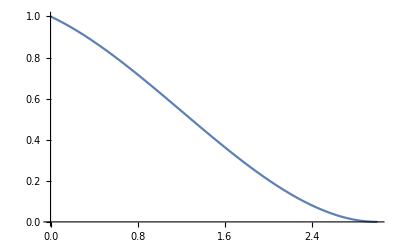

```mathematica
Module[
{a = -0.25, b = 3},
Plot[InterpolatingPolynomial[{{0, 1, a}, {b, 0, 0}}, x], {x, 0, b}]
]
```

```mathematica
T =6.0;
Tmax = 0.9T;
αMax = 6.5;
```

{{0.0462051,-0.0472078,1.99891},{1.21782,1.05561,1.02833}}

{{-1.73964,-0.469897,1.30517},{0.270723,0.50442,0.765954}}

{{-2.2728,0.901782,1.65142},{0.0533746,0.498306,0.527341}}

{{-2.56705,1.46877,2.51039},{0.0179606,0.284618,0.275132}}

{{-2.97492,1.24603,3.5741},{0.00300403,0.25425,0.251248}}

{{-3.2521,-0.312335,5.61928},{0.413546,0.369038,0.0575765}}

{{-3.7351,-0.427584,5.11123},{0.0689946,0.0711241,0.0124415}}

{{-4.01395,-0.412747,4.51622},{0.0077988,0.0261607,0.0183633}}

{{-4.08225,-0.519138,4.05137},{0.000807691,0.0129256,0.0128463}}

{{-4.05328,-0.639226,3.85801},{0.00019636,0.00424391,0.00441074}}

{{-4.02907,-0.692534,3.7832},{0.0000535415,0.0011568,0.00120979}}

{{-4.01583,-0.71662,3.74928},{0.0000141085,0.000298717,0.000312659}}

{{-4.00951,-0.725233,3.73524},{3.48109×10^-6,0.0000747343,0.0000782513}}

{{-4.00528,-0.734956,3.72402},{1.85955×10^-6,0.0000195911,0.0000194317}}

{{-4.00404,-0.735145,3.72205},{4.22331×10^-7,4.68448×10^-6,4.65215×10^-6}}

{{-4.00344,-0.735243,3.72106},{8.02422×10^-8,1.04487×10^-6,1.04161×10^-6}}

{{-4.00315,-0.735308,3.72053},{4.74833×10^-9,1.82918×10^-7,1.85018×10^-7}}

{{-4.00305,-0.735357,3.72021},{-4.51194×10^-9,6.44018×10^-9,7.45213×10^-9}}

{{-4.00306,-0.735353,3.7201},{6.13643×10^-10,1.6169×10^-9,1.50704×10^-9}}

{{-4.00306,-0.735354,3.7201},{-1.33676×10^-10,-6.27796×10^-10,-6.06126×10^-10}}

{{-4.00306,-0.735354,3.7201},{4.14797×10^-11,1.95835×10^-10,1.89173×10^-10}}

{-4.00306,-0.735354,3.7201}

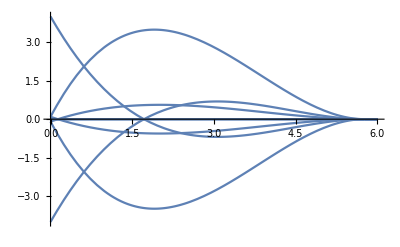

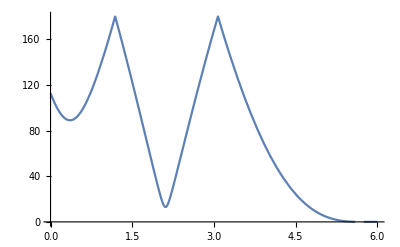

0.00118325

```mathematica
α = ωTargetIterative[θ0, θTarget, ω0, T]
soln = First[NDSolve[{Y'[t] == A[ω0, α, t].Y[t], Y[0]==θ0}, Y, {t, 0,T}]];
Plot[A[ω0, α, t], {t,0,T}, PlotRange->All]
Plot[AngleBetween[θTarget,Y[t] /. soln] 180/π, {t,0,T}, PlotRange->All]
AngleBetween[θTarget,Y[T] /. soln] * 180/π
```

```mathematica
Tr[{{0.01294190044021093,0.015903602212929968,0.0033621090356206196},{0.015903602212929968,-0.09758293906259041,-0.016321497708915444},{0.0033621090356206196,-0.016321497708915444,0.012732079834876231}}]
```

-0.071909

```mathematica
ωTargetHessian[θ0_, θ1_, {ω0x_, ω0y_, ω0z_}, T_] := Module[{
ω0 = {ω0x, ω0y, ω0z},
α = {0, 0, 0},
eye = IdentityMatrix[3],
ϵ = 0.001,
r, 
R, 
gradR = ConstantArray[0.0, 3], 
HR = ConstantArray[0.0, {3,3}]
},

r[αTrial_] := 3- Tr[θ1.Transpose[Y[T] /. First[NDSolve[{Y'[t] == A[ω0, αTrial, t].Y[t], Y[0]==θ0}, Y, {t, 0,T}]]]];

Do[
R = Table[r[α + {i, j, k} ϵ], {i, -1, 1}, {j, -1, 1},{k, -1, 1}];
Print[{R[[2,2,2]], α}];
gradR = {(R[[3,2,2]]-R[[1,2,2]])/(2ϵ), (R[[2,3,2]] - R[[2,1,2]])/(2ϵ), (R[[2,2,3]] - R[[2,2,1]])/(2ϵ)};
HR[[1,1]]= (R[[3,2,2]]-2R[[2,2,2]]+R[[1,2,2]])/ϵ^2;
HR[[2,2]]= (R[[2,3,2]]-2R[[2,2,2]]+R[[2,1,2]])/ϵ^2;
HR[[3,3]]= (R[[2,2,3]]-2R[[2,2,2]]+R[[2,2,1]])/ϵ^2;
HR[[1,2]]=HR[[2,1]]= (R[[3,3,2]]+R[[1,1,2]]-R[[1,3,2]]-R[[3,1,2]])/(4 ϵ^2);
HR[[1,3]]=HR[[3,1]]= (R[[3,2,3]]+R[[1,2,1]]-R[[1,2,3]]-R[[3,2,1]])/(4 ϵ^2);
HR[[2,3]]=HR[[3,2]]= (R[[2,3,3]]+R[[2,1,1]]-R[[2,1,3]]-R[[2,3,1]])/(4 ϵ^2);
Print[HR];
If[Tr[HR] < 0, HR -= 1.5 Tr[HR]/3 eye ];
α-=LinearSolve[HR, gradR];
α*=Min[1.0, αMax/Norm[α]];
,
{i, 1, 10}
];
Print[r[α]];
α
]
```

```mathematica
ωTargetIterative[θ0_, θ1_, {ω0x_, ω0y_, ω0z_}, T_] := Module[{
ω0 = {ω0x, ω0y, ω0z},
ωAvg = rotationAxis[θ1.Transpose[θ0]],
α = -0.5{ω0x, ω0y, ω0z},
eye = IdentityMatrix[3],
ϵ = 0.0001,
Tmax = 0.8T,
αMax = 6.5,
r, J
},
r[αTrial_]:=({1, 1, 1} - Diagonal[θ1.Transpose[Y[T] /. First[NDSolve[{Y'[t] == A[ω0, αTrial, t].Y[t], Y[0]==θ0}, Y, {t, 0,T}]]]]);
Do[
Print[{α, r[α], Tmax}];
J =Transpose[(r[α + ϵ #] - r[α])/ϵ& /@ eye];
α -= LinearSolve[J, r[α]];
If[Norm[α] > αMax, 
Tmax *= 1.2;
α*=αMax/Norm[α];
],
{i, 1, 20}
];
Print[{α, r[α], Tmax}];
{α, Tmax}
]
```

```mathematica
Magnus[t_] := Module[{a0, a1},
a0 = If[t < τ,A[t/2],τ/t A[τ/2] + (1 - τ/t)A[τ]];
a1 = (A[t] - A[0])/t;
t a0 - t^3/12 Comm[a0, a1]-t^5/240 Comm[a1, Comm[a0, a1]]
]
```

```mathematica
MagnusLinear[t_] := Module[{A0, A1, A2, α1, α2, α3},
{A0, A1, A2} = Ω /@{1/6 t (-ω0 (-6+t)+ω1 t),1/36 (-ω0+ω1) t^2,1/72 t (-ω0 (-6+t)+ω1 t)};
α1 = 9/4 A0-15A2;
α2 = 12 A1;
α3 = -15 A0 + 180 A2;

α1 + 1/12 α3 - 1/12 Comm[α1, α2] + 1/240 Comm[α2, α3] + 
1/360 Comm[α1, Comm[α1, α3]] - 1/240 Comm[α2,Comm[α1, α2]]+1/720 Comm[α1, Comm[α1, Comm[α1, α2]]]
]
```

```mathematica
Table[
FullSimplify[1/tf^i Integrate[(t-tf/2)^i(a0 (1 - t/τ) + a1 t/τ), {t, 0, tf}], Assumptions->{i ≥ 0, τ > tf > 0}],
{i, 0, 2}
]
```

```mathematica
ωTargetIterative[θ0_, θ1_, {ω0x_, ω0y_, ω0z_}, T_, τ_] := Module[{
ω0 = {ω0x, ω0y, ω0z},
ωAvg = rotationAxis[θ1.Transpose[θ0]],
ωGuess = {0, 0, 0},
eye = IdentityMatrix[3],
ϵ = 0.01,
r, J
},
r[ω1_] := ωAvg-rotationAxis[Y[1] /. First[NDSolve[{Y'[t] == (Ω[ω0] (1 - t/τ) + Ω[ω1] t/τ).Y[t], Y[0] == θ0}, Y, {t, 0,T}]]]+ ωGuess;

Do[
Print[r[ωGuess]];
J=Transpose[(r[ωGuess + ϵ #] - r[ωGuess])/ϵ& /@ eye];
ωGuess -= 1/2 LinearSolve[J, r[ωGuess]];
,
{i, 1, 10}
];
Print[r[ωGuess]];
ωGuess
]
```

{-3.74504,-0.813225,1.3919}

{-1.94686,-0.971857,0.695494}

{-0.891236,-0.737932,0.306099}

{-0.382051,-0.457264,0.123176}

{-0.167172,-0.251967,0.0505991}

{-0.076836,-0.131626,0.0221734}

{-0.0366519,-0.0672165,0.0102367}

{-0.0178694,-0.0339782,0.00487961}

{-0.00881516,-0.0170945,0.00236756}

{-0.00437519,-0.0085805,0.00115947}

{-0.00217828,-0.00430207,0.000570528}

{-4.58204,-0.16484,-5.13895}

{{Y→InterpolatingFunction[…]}}

2.56142

1.24703

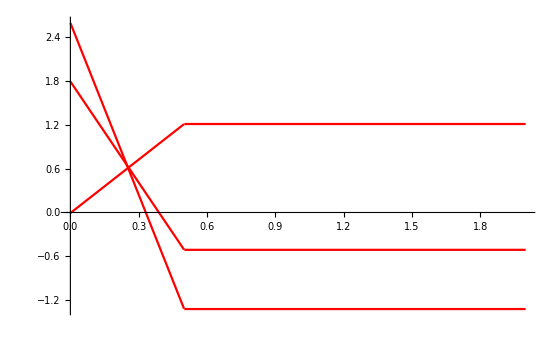

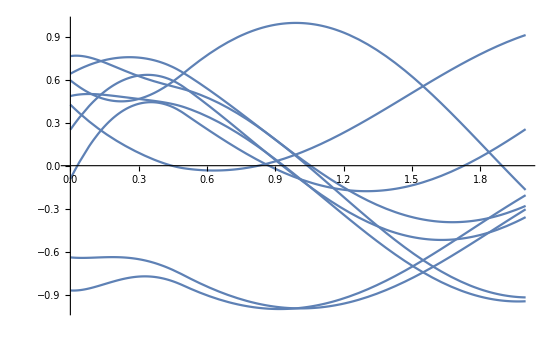

```mathematica
A[t_] := Ω[ω0] Max[1-t/τ, 0] + Ω[ω1]Min[1,t/τ] 
soln= NDSolve[{Y'[t] == A[t].Y[t], Y[0] == θ0}, Y, {t, 0,T}]

AngleBetween[θ0, θTarget] 
AngleBetween[First[Y[T] /. soln], θTarget] 

Plot[Flatten[axis[A[t]]], {t, 0, T}, PlotStyle->Red]

Show[
Plot[{Y[t] /.soln}, {t, 0, T}]
]
```

```mathematica
ωTargetMagnus[θ0_, θ1_, {ω0x_, ω0y_, ω0z_}, T_, τ_] := Module[{
ωAvg = rotationAxis[θ1.Transpose[θ0]],
A, b
},
If[T < τ,
A = {{T^2/(2 τ),(T^3 ω0z)/(12 τ),-(T^3 ω0y)/(12 τ)},{-(T^3 ω0z)/(12 τ),T^2/(2 τ),(T^3 ω0x)/(12 τ)},{(T^3 ω0y)/(12 τ),-(T^3 ω0x)/(12 τ),T^2/(2 τ)}};
b = ωAvg-{T ω0x-(T^2 ω0x)/(2 τ),T ω0y-(T^2 ω0y)/(2 τ),T ω0z-(T^2 ω0z)/(2 τ)};
,
A = {{T-τ/2,(T^2 ω0z)/12,-(T^2 ω0y)/12},{-(T^2 ω0z)/12,T-τ/2,(T^2 ω0x)/12},{(T^2 ω0y)/12,-(T^2 ω0x)/12,T-τ/2}};
b = ωAvg-{(τ ω0x)/2,(τ ω0y)/2,(τ ω0z)/2};
];
LinearSolve[A, b]
]
```

```mathematica
Magnus3[t_] := Module[{A0, A1, A2, α1, α2, α3},
A0 = Quiet[Integrate[A[tf], {tf, 0, t}]];
A1 = 1/t Quiet[Integrate[(tf - t/2)A[tf], {tf, 0, t}]];
A2 = 1/t^2 Quiet[Integrate[(tf - t/2)^2 A[tf], {tf, 0, t}]];
α1 = 9/4 A0-15A2;
α2 = 12 A1;
α3 = -15 A0 + 180 A2;

α1 + 1/12 α3 - 1/12 Comm[α1, α2] + 1/240 Comm[α2, α3] + 
1/360 Comm[α1, Comm[α1, α3]] - 1/240 Comm[α2,Comm[α1, α2]]+1/720 Comm[α1, Comm[α1, Comm[α1, α2]]]
]
```

```mathematica
soln= NDSolve[{Y'[t] == A[t].Y[t], Y[0] == IdentityMatrix[3]}, Y, {t, 0, 1}]
```

{{Y→InterpolatingFunction[…]}}

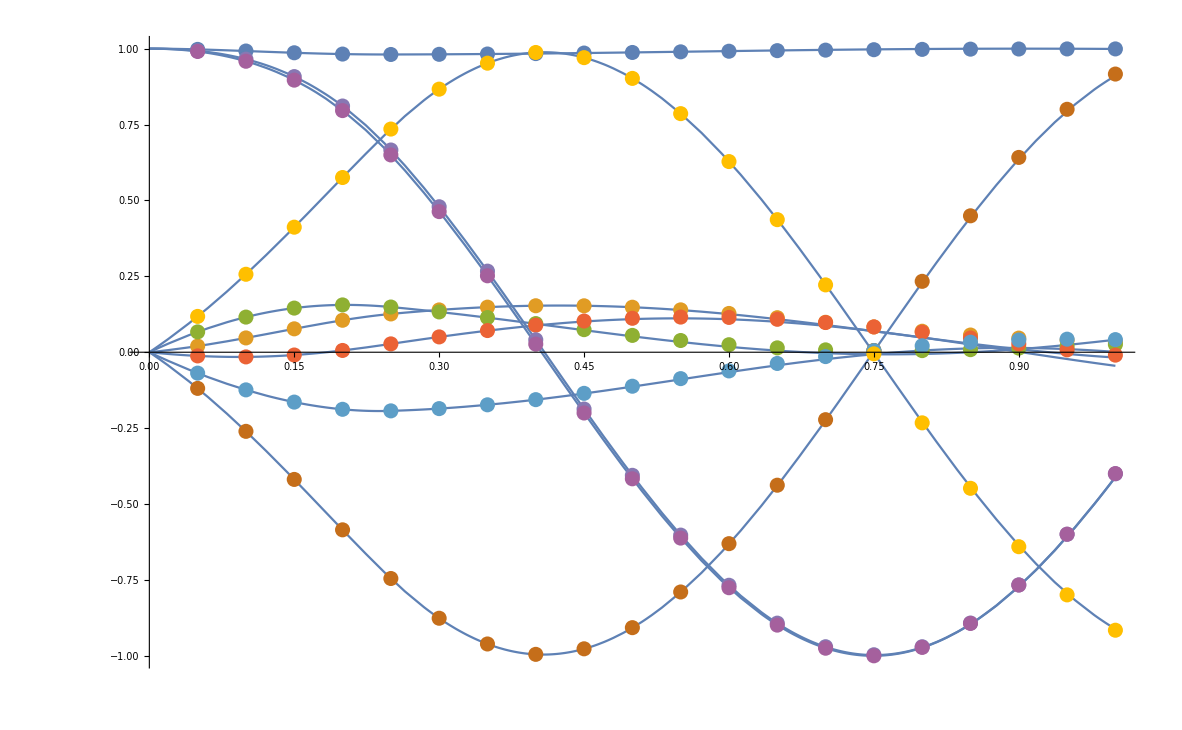

```mathematica
Show[
Plot[Y[t] /.soln, {t, 0, 1}],
ListPlot[Transpose[Table[Flatten[MatrixExp[MagnusLinear[t]]], {t, 0.05, 1, 0.05}]], DataRange->{0.05, 1}]
]
```

```mathematica
θ1 = First[Y[1] /.soln]
```

{{0.02637,-0.864557,-0.501842},{0.172461,-0.490554,0.854174},{-0.984663,-0.109073,0.136166}}

```mathematica
θ2 = MatrixExp[Magnus[1]]
```

{{-0.123203,-0.907186,-0.402287},{0.314429,-0.420174,0.851227},{-0.941252,-0.0216169,0.337012}}

```mathematica
AngleBetween[θ1, θ2] * 180/π
```

13.4119

```mathematica
ϵ = 0.001;
```

```mathematica
f[{ξ_, η_, ζ_}] := Sin[2 π (ξ - 2η) ζ]
```

```mathematica
HR = ConstantArray[0, {3,3}]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
samples = Table[{ξ, η, ζ} + {i, j, k} ϵ, {i, -1, 1}, {j, -1, 1},{k, -1, 1}]
```

1
 |  |  |  |

```mathematica
samples[[3,2,2]]
```

{-0.611886,-0.880471,0.771546}

```mathematica
ξ
```

-0.612886

```mathematica
η
```

-0.880471

```mathematica
ζ
```

0.771546

```mathematica
R = Table[f[{ξ, η, ζ} + {i, j, k} ϵ], {i, -1, 1}, {j, -1, 1},{k, -1, 1}];
gradR = {(R[[3,2,2]]-R[[1,2,2]])/(2ϵ), (R[[2,3,2]] - R[[2,1,2]])/(2ϵ), (R[[2,2,3]] - R[[2,2,1]])/(2ϵ)};
HR[[1,1]]= (R[[3,2,2]]-2R[[2,2,2]]+R[[1,2,2]])/ϵ^2;
HR[[2,2]]= (R[[2,3,2]]-2R[[2,2,2]]+R[[2,1,2]])/ϵ^2;
HR[[3,3]]= (R[[2,2,3]]-2R[[2,2,2]]+R[[2,2,1]])/ϵ^2;
HR[[1,2]]=HR[[2,1]]= (R[[3,3,2]]+R[[1,1,2]]-R[[1,3,2]]-R[[3,1,2]])/(4 ϵ^2);
HR[[1,3]]=HR[[3,1]]= (R[[3,2,3]]+R[[1,2,1]]-R[[1,2,3]]-R[[3,2,1]])/(4 ϵ^2);
HR[[2,3]]=HR[[3,2]]= (R[[2,3,3]]+R[[2,1,1]]-R[[2,1,3]]-R[[2,3,1]])/(4 ϵ^2);
```

```mathematica
{ξ, η, ζ} = RandomReal[{-1, 1}, 3]
```

{-0.612886,-0.880471,0.771546}

```mathematica
gradR- D[f[{x, y, z}], {{x, y, z}}]/. {x->ξ, y ->η, z->ζ}
```

{-0.0000143042,0.000114433,-0.0000471265}

```mathematica
HR - D[f[{x, y, z}], {{x, y, z}, 2}] /. {x->ξ, y ->η, z->ζ}
```

{{-0.0000302671,0.000605338,-0.000468274},{0.000605338,-0.000484273,0.00181069},{-0.000468274,0.00181069,-0.00014838}}

```mathematica
HR
```

{{15.455,-30.9094,27.7298},{-30.9094,61.8195,-55.4588},{27.7298,-55.4588,34.2191}}

```mathematica
Plot3D[f[{x, y, z}], {x, -2, 2}, {y, -2, 2}]
```

-Graphics3D-